```mathematica
Clear[D2]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
D2[n_, k_] := D2[n,k]=Sum[ D2[Floor[n/j],k-1],{j,2,n}]; D2[n_, 0]:= UnitStep[n-1]
d2[n_, k_] := D2[n,k]-D2[n-1,k]
Dz[n_, z_] := Sum[ bin[ z,k]D2[n,k],{k,0,Log[2,n]}]
Ez[n_, t_] := Sum[ Dz[n,k]/k!,{k,0,t}]
ez[n_, t_] := Ez[n,t]-Ez[n-1,t]
Ez2[n_] := Sum[ D2[n,k]/k!,{k,0,Log[2,n]}]
ez2[n_] := Ez2[n]-Ez2[n-1]
Sn[n_, t_] := Sn[n,t]=Sum[(D[Sin[ x ],{x,k}]/.x->0)/k! Dz[n,k],{k,0,t}]
Cs[n_, t_] := Cs[n,t]=Sum[(D[Cos[ x ],{x,k}]/.x->0)/k! Dz[n,k],{k,0,t}]
sn[n_, t_] := Sn[n,t]-Sn[n-1,t]
cs[n_, t_] := Cs[n,t]-Cs[n-1,t]
Sn2[n_] := Sn2[n]=Sum[(D[Sin[ x ],{x,k}]/.x->0)/k! D2[n,k],{k,0,Log[2,n]}]
Cs2[n_] := Cs2[n]=Sum[(D[Cos[ x ],{x,k}]/.x->0)/k! D2[n,k],{k,0,Log[2,n]}]
sn2[n_] := Sn2[n]-Sn2[n-1]
cs2[n_] := Cs2[n]-Cs2[n-1]
l[n_, z_] :=LaguerreL[-z,Log[n]]
l2[n_, z_] := (-1)^(z)Gamma[z,0,-Log[n]]/Gamma[z]
lEz[n_, t_] := Sum[ l[n,k]/k!,{k,0,t}]
lEz2[n_,t_] := 1+Sum[l2[n,k]/k!,{k,1,t}]
lSn[n_, t_] := lSn[n,t]=Sum[(D[Sin[ x ],{x,k}]/.x->0)/k! l[n,k],{k,0,t}]
lCs[n_, t_] := lCs[n,t]=Sum[(D[Cos[ x ],{x,k}]/.x->0)/k! l[n,k],{k,0,t}]
lSn2[n_,t_] := lSn2[n]=Sum[(D[Sin[ x ],{x,k}]/.x->0)/k! l2[n,k],{k,0,t}]
lCs2[n_,t_] := lCs2[n]=Sum[(D[Cos[ x ],{x,k}]/.x->0)/k! l2[n,k],{k,0,t}]
```

```mathematica
N@Sum[ cs[j,30]cs[k,30],{j,1,100},{k,1,100/j}]+Sum[ sn[j,30]sn[k,30],{j,1,100},{k,1,100/j}]
```

1.

```mathematica
N@Sum[ cs2[j]cs2[k],{j,1,100},{k,1,100/j}]+Sum[ sn2[j]sn2[k],{j,1,100},{k,1,100/j}]
```

1.

```mathematica
2N@Sum[sn[j,30]cs[k,30],{j,1,100},{k,1,100/j}]
```

-311.06

```mathematica
N@Sn[2 100,30]
```

-249.411

```mathematica
2N@Sum[sn2[j]cs2[k],{j,1,100},{k,1,100/j}]
```

-220.4

```mathematica
N@Sn2[100]
```

45.425

```mathematica
N@lEz[10,15]/N@lEz2[10,15]
```

2.71828+2.43642×10^-16 ⅈ

```mathematica
N@lEz[13,15]/N@lEz2[13,15]
```

2.71828+2.83305×10^-16 ⅈ

```mathematica
N@lEz[3I,40]
```

-5.63354+7.4274 ⅈ

```mathematica
N[lCs[3,40]+I lSn[3, 40]]
```

-1.41744+1.33588 ⅈ

```mathematica
Clear[ff,ff2, gg2]
(*ff[ n_] := ff[n]=Sum[ (Floor[j^(1/2)]-Floor[(j-1)^(1/2)]) MoebiusMu[k],{j,1,n},{k,1,n/j}]*)
fn[j_] := ((Floor[j^(2/3)]-Floor[(j-1)^(2/3)]))
ff[ n_] := ff[n]=Sum[ fn[j]fn[k] ,{j,1,n},{k,1,n/j}]
ffd[n_] := ff[n]-ff[n-1]
ff2[n_, k_] := ff2[n,k]=Sum[ fn[j]ff2[Floor[n/j],k-1],{j,2,n}]
ff2[n_, 0] := UnitStep[n-1]
ffl[n_] := Sum[ (-1)^(k+1)/k ff2[n,k],{k,1,Log2@n}]
gg2[n_, k_] := gg2[n,k]=Sum[fn[j]gg2[Floor[n/j],k-1],{j,2,n}]
gg2[n_, 0] := UnitStep[n-1]
ggl[n_] := Sum[ (-1)^(k+1)/k gg2[n,k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
```

```mathematica
Table[ ffl[n]-ffl[n-1],{n,1,20}]
```

{0,0,1,0,0,1,0,1,-1/2,0,0,1,0,0,1,0,0,-1,1,0}

```mathematica
Table[ LiouvilleLambda[n],{n,2,20}]
```

{-1,-1,1,-1,1,-1,-1,1,1,-1,-1,-1,1,1,1,-1,-1,-1,-1}

```mathematica
fg[n_] := Sum[ j*MoebiusMu[k],{j,1,n},{k,1,n/j}]
```

```mathematica
fg[100]-fg[99]
```

40

```mathematica
EulerPhi[100]
```

40

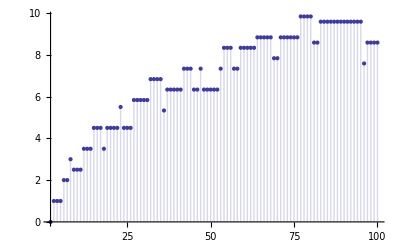

```mathematica
DiscretePlot[ffl[n] ,{n,2,100}]
```

```mathematica
Log[ (1-x^(1-s))Zeta[s]]/.{x->2,s->2}
```

Log[π^2/12]

```mathematica
N@Log[ (1-x^(1-s))Zeta[s]^2]/.{x->2,s->2}
```

0.302253

```mathematica
N@2 Log[ (1-x^(1-s))^(1/2)Zeta[s]]/.{x->2,s->2}
```

0.302253

```mathematica
Log[a b^c]
```

Log[a b^c]

```mathematica
N@Log[ (1-x^(1-s))]+2Log[Zeta[s]]/.{x->2,s->2}
```

0.302253

```mathematica
FullSimplify@Sum[ -x^(k(1-s))/k,{k,1,Infinity}]
```

Log[1-x^(1-s)]

```mathematica
FullSimplify@Sum[ - x^(k(1-s))/k,{k,1,Infinity}]
```

Log[1-x^(1-s)]

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]

Clear[fk]
fk[n_, z_, k_] := fk[n,z,k]=Sum[ (-1)^(j+1)dz[j,2] fk[Floor[n/j],z,k-1],{j,2,n}]
fk[n_, z_, 0] := UnitStep[n-1]
fl[n_, z_] := Sum[ (-1)^(k+1)/k fk[n,z,k],{k,1,Log2@n}]
```

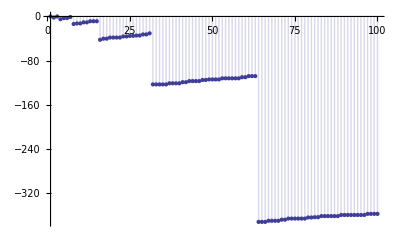

```mathematica
DiscretePlot[ fl[n,1], {n,1,100}]
```

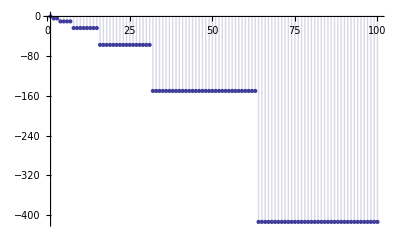

```mathematica
DiscretePlot[ fl[n,2]-2pr[n], {n,1,100}]
```

```mathematica
ad[n_] := -Sum[ 2^k 2 dz[2,-1 k]/k,{k,1,Log[2,n]}]
```

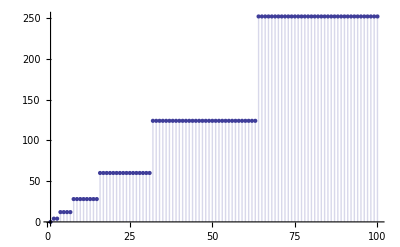

```mathematica
DiscretePlot[ad[n], {n,1,100}]
```

```mathematica
Clear[D1xD,E2,Dz]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
Dz[n_,z_,z2_, k_]:=Dz[n,z,z2,k]=1+((z+1)/k-1)Sum[dz[j,z2]Dz[Floor[n/j],z,z2,k+1],{j,2,n}]
E2[n_,k_]:=E2[n,k]=Sum[(-1)^(j+1)  E2[Floor[n/j],k-1],{j,2,n}];E2[n_,0]:=UnitStep[n-1]
Etz[n_, z_] := Sum[ bin[ z,k]E2[n,k],{k,0,Log[2,n]}]
etz[n_, z_] := Etz[n,z]-Etz[n-1,z]
D1xD[n_,k_,z2_]:=D1xD[n,k,z2]=Sum[etz[j,z2]  D1xD[n/j,k-1,z2],{j,2,n}];D1xD[n_,0,z2_]:=UnitStep[n-1]
E1[n_, z_] := Sum[ (-1)^(k+1)/k D1xD[n,k,z],{k,1,Log2@n}]
D1xDa[n_, k_, z2_] := Sum[ (-1)^(k-j)bin[k,j]Etz[n,j z2],{j,0,k}]
D1xDbo[n_, k_, z2_] := Sum[ (-1)^(k-j)bin[k,j]Sum[ bin[ j z2,r]E2[n,r],{r,0,Log[2,n]}],{j,0,k}]
D1xDb[n_, k_, z2_] := Sum[ (-1)^(k-j)bin[k,j]bin[ j z2,r]E2[n,r],{j,0,k},{r,0,Log[2,n]}]
D1xDb1[n_, k_, z2_] := Sum[ E2[n,r]Sum[(-1)^(k-j)bin[k,j]bin[ j z2,r],{j,0,k}],{r,0,Log[2,n]}]
D1xF[n_, k_, z_] := Sum[ (-1)^(k-j)bin[k,j]bin[ j z,r]E2[n,r],{j,0,k},{r,0,Log[2,n]}]
DzAlt[n_,z_,z2_]:=Sum[(-1)^j bin[-z,j]bin[z,k] 2^j  D1xD[n/2^j,k,z2],{j,0,Log[2,n]},{k,0,Log[2,n/2^j]}]
D2x[n_, k_, z_] := Sum[ (-1)^(k-j)bin[k,j]bin[ j z,r]D2[n,r],{j,0,k},{r,0,Log[2,n]}]
```

```mathematica
{Etz[121,6]-2Etz[121,3]+1,D1xD[121,2,3], D1xDa[121,2,3], D1xDb1[121,2,3]}
```

{301,301,301,301}

```mathematica
{Etz[121,3 2.3]-3Etz[121,2 2.3]+3Etz[121,2.3]-1,D1xD[121,3,2.3], D1xDa[121,3,2.3], D1xDb1[121,3,2.3]}
```

{153.061,153.061,153.061,153.061}

```mathematica
Dz[100,2,3,1]
```

14393

```mathematica
Dz[100,6,1,1]
```

14393

```mathematica
Dz[100,1,6,1]
```

14393

```mathematica
Sum[ dz[j,2]dz[k,2],{j,2,100},{k,2,100/j}]
```

2612

```mathematica
Sum[ 1, {j,1,100},{k,1,100/j},{l,1,100/(j k)},{m,1,100/(j k l)}]-2Sum[ 1, {j,1,100},{k,1,100/j}]+1
```

2612

```mathematica
Expand[(x^2-1)^2]
```

1-2 x^2+x^4

```mathematica
Etz[100,4]-2Etz[100,2]+1
```

-12

```mathematica
Sum[etz[j,2]etz[k,2],{j,2,100},{k,2,100/j}]
```

-12

```mathematica
Sum[ (-1)^(j+k+l+m), {j,1,100},{k,1,100/j},{l,1,100/(j k)},{m,1,100/(j k l)}]-2(Sum[ (-1)^(j+k), {j,1,100},{k,1,100/j}])+1
```

-12

```mathematica
Sum[ (-1)^(j+k+l+m), {j,1,100},{k,1,100/j},{l,1,100/(j k)},{m,1,100/(j k l)}]-2(Sum[ 1, {j,1,100},{k,1,100/j}]-2 2Sum[ 1, {j,1,50},{k,1,50/j}]+4Sum[ 1, {j,1,25},{k,1,25/j}])+1
```

-12

```mathematica
Sum[ (-1)^(j+k+l+m), {j,1,100},{k,1,100/j},{l,1,100/(j k)},{m,1,100/(j k l)}]-2(Dz[100,2,1,1]-2 2Dz[50,2,1,1]+4Dz[25,2,1,1])+1
```

-12

```mathematica
Sum[ (-1)^(j+k+l+m), {j,1,100},{k,1,100/j},{l,1,100/(j k)},{m,1,100/(j k l)}]-
2(Dz[100,2,1,1]-2 2Dz[50,2,1,1]+4Dz[25,2,1,1])+1
```

-12

```mathematica
(Dz[100,4,1,1]-2 4Dz[50,4,1,1]+4 6Dz[25,4,1,1]-8 4Dz[12,4,1,1]+16 Dz[6,4,1,1])-
2(Dz[100,2,1,1]-2 2Dz[50,2,1,1]+4Dz[25,2,1,1])+1
```

-12

```mathematica
Sum[etz[j,3]etz[k,3],{j,2,100},{k,2,100/j}]
```

-116

```mathematica
Etz[100,6]-2Etz[100,3]+1
```

-116

```mathematica
Sum[etz[j,-5/2]etz[k,-5/2],{j,2,100},{k,2,100/j}]
```

-1093425/512

```mathematica
Etz[100,-5]-2Etz[100,-5/2]+1
```

-1093425/512

```mathematica
Sum[etz[j,3]etz[k,3]etz[l,3],{j,2,100},{k,2,100/j},{l,2,100/(j k)}]
```

-189

```mathematica
Etz[100,9]-3Etz[100,6]+3 Etz[100,3]-1
```

-189

```mathematica
Sum[etz[j,x]etz[k,x]etz[l,x],{j,2,100},{k,2,100/j},{l,2,100/(j k)}]/.x->(3)
```

-189

```mathematica
Sum[etz[j,x]etz[k,x],{j,2,100},{k,2,100/j}]/.x->(3)
```

-116

```mathematica
bb[n_, k_, x_] := Sum[ (-1)^(k-j) bin[k,j]Etz[n,j x],{j,0,k}]
bc[n_, k_, x_] := Sum[ (-1)^(k-j) bin[k,j]bin[ j x,r]E2[n,r],{j,0,k},{r,0,Log[2,n]}]
bd[n_, z_, x_] := Sum[ bin[ z,k] Sum[ (-1)^(k-j) bin[k,j]bin[ j x,r]E2[n,r],{j,0,k},{r,0,Log[2,n]}],{k,0,Log[2,n]}]
```

```mathematica
bc[100,2,3]
```

-116

```mathematica
bd[100,2,7]
```

-5361

```mathematica
D1xD[100,2,7]
```

-5782

```mathematica
Etz[100,14]
```

-6201

```mathematica
etz[100,1]
```

-1

```mathematica
D1xDb1a[n_, k_, z2_] := Table[ Sum[(-1)^(k-j)bin[k,j]bin[ j z2,r],{j,0,k}],{r,0,Log[2,n]}]
D1xDb1a[1208,1,5]
```

{0,5,10,10,5,1,0,0,0,0,0}

```mathematica
{Dz[121,6,1,1]-2Dz[121,3,1,1]+1,D2x[121,2,3]}
```

{16213,16213}

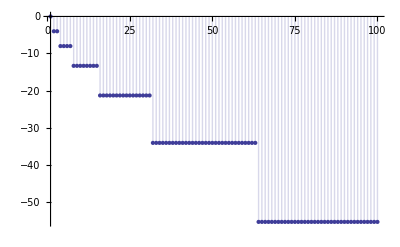

```mathematica
DiscretePlot[ (E1[n,2]-2pr[n]),{n,1,100}]
```

```mathematica
fo[n_] := -Sum[ 2^k/k,{k,1,Log2@n}]
```

```mathematica
fo[100]
```

-416/15

```mathematica
DiscretePlot[ 2fo[n],{n,1,100}]
```

-Graphics-

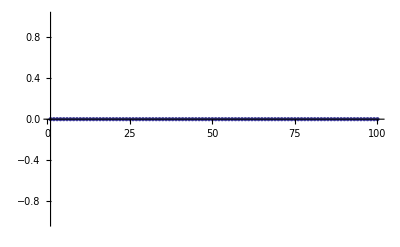

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
E2[n_,k_]:=E2[n,k]=Sum[(-1)^(j+1)  E2[Floor[n/j],k-1],{j,2,n}];E2[n_,0]:=UnitStep[n-1]
Etz[n_, z_] := Sum[ bin[ z,k]E2[n,k],{k,0,Log[2,n]}]
etz[n_, z_] := Etz[n,z]-Etz[n-1,z]
D1xD[n_,k_,z2_]:=D1xD[n,k,z2]=Sum[etz[j,z2]  D1xD[n/j,k-1,z2],{j,2,n}];D1xD[n_,0,z2_]:=UnitStep[n-1]
E1[n_, z_] := Sum[ (-1)^(k+1)/k D1xD[n,k,z],{k,1,Log2@n}]
fo[n_] := -Sum[ 2^k/k,{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
DiscretePlot[ E1[n,2]-(2pr[n]+2fo[n]),{n,1,100}]
```